```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
<<"HeterogeneousTemplate.wl";

GenerateMarkovTemplates[  MarkovProc_, NumTemplates_, LenTemplates_ ] :=
	(RandomFunction[MarkovProc,{#,LenTemplates}][[2]][[1]][[1]])&/@ConstantArray[1,NumTemplates];

FreeEnergyAvg[inputtemplates_,EnergyMatrix_] := Mean[FreeEnergy[#,EnergyMatrix] &/@ inputtemplates];

EqFreeEnergy[  inputtemplate_,EnergyMatrix_,Fmin_ ] :=
	Log[PartitionFunc[Exp[Fmin+EnergyMatrix],
		Exp[EnergyMatrix[[1]][[2]][[;;]][[1]]],Exp[EnergyMatrix[[1]][[2]][[;;]][[2]]],
		inputtemplate]];
```

{{2.,0},{0,2.}}

{{2.,0},{0,4.}}

{{2.,0},{0,6.}}

{{2.,0},{0,8.}}

{{2.,0},{0,10.}}

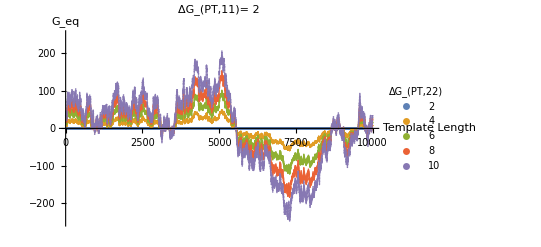

```mathematica
copysize= 2;
templatesize = 2;
(*masterTemplate = RandomChoice[{0.5,0.5}->{1,2},10000];*)
Get["masterTemplate"];
domainLengths = Range[2,10000];
Domain = masterTemplate[[1;;#]] &/@ domainLengths;
KineticMatrix = {{0.0,0.0},{0.0,0.0}};
FEData = {};

For [ x = 2.0,x<10.1,x = x+2.0,
	BaseEnergyMatrix =  {{2.0,0},{0,x}};
	Print[BaseEnergyMatrix];
	(*EnergyMatrix Takes into account corrections due to bases being placed after correct or incorrect pairs*)
		EnergyMatrix = ConstantArray[0.0,{2,2,2,2}];
		For [i = 1, i<= 2, i++,
			For [d = 1, d<= 2, d++,
				For [j = 1, j<= 2, j++,
					EnergyMatrix[[i]][[d]][[j]][[j]] = BaseEnergyMatrix[[j]][[j]];
				]
			]		
		];
	Fmin = -Log[PartitionFunc[Exp[EnergyMatrix],
		Exp[EnergyMatrix[[1]][[2]][[;;]][[1]]],Exp[EnergyMatrix[[1]][[2]][[;;]][[2]]],
		masterTemplate]]/(Length[masterTemplate]);
	MeanFE =EqFreeEnergy[#,EnergyMatrix,Fmin]  &/@ Domain;
	MeanFE = MeanFE-Mean[MeanFE];
	FEData =Append[FEData,Transpose@{domainLengths,MeanFE}];
]

mu={2,4,6,8,10};
pl=PointLegend[mu,LegendLabel->Subscript["ΔG","PT,22"],LegendFunction->"Frame",LegendLayout->Automatic,LegendMarkers->Automatic];
p1 =ListPlot[FEData,AxesLabel->{"Template Length",Subscript["G","eq"]},
		PlotLegends->Placed[pl,Right], PlotRange -> {{1,10000},{-250,250}},PlotLabel->Row[{Subscript["ΔG","PT,11"],"= 2"}]]
```

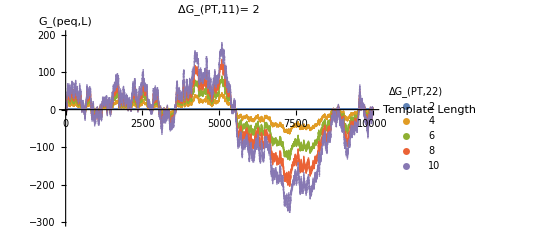

```mathematica
mu={2,4,6,8,10};
pl=PointLegend[mu,LegendLabel->Subscript["ΔG","PT,22"],LegendFunction->"Frame",LegendLayout->Automatic,LegendMarkers->Automatic];
p1 =ListPlot[FEData,AxesLabel->{"Template Length",Subscript["G","peq,L"]},
		PlotLegends->Placed[pl,Right], PlotRange -> {{1,10000},{-300,200}},PlotLabel->Row[{Subscript["ΔG","PT,11"],"= 2"}]]
```

```mathematica
Save["PermTherm.FreeEnergyData.Deviation",FEData]
(*Save["masterTemplate",masterTemplate]*)
```

-5.533773810444821717145571938967888892217799936889207292766873892220477210140737598730922082404670422321068

{-5.6,-5.533773810444821717145571938967888892217799936889207292766873892220477210140737598730922082404670422321068,-5.4,-5.2,-5.,-4.8,-4.6,-4.4,-4.2,-4.,-3.8,-3.6,-3.4,-3.2,-3.,-2.8,-2.6,-2.4,-2.2,-2.,-1.8,-1.6,-1.4,-1.2,-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

```mathematica
Ceiling[Fmin,0.5]
```

-2.

```mathematica
For [ x = 2.0,x<10.1,x = x+2.0,
	BaseEnergyMatrix =  {{2.0,0},{0,x}};
	Print[BaseEnergyMatrix];
	(*EnergyMatrix Takes into account corrections due to bases being placed after correct or incorrect pairs*)
		EnergyMatrix = ConstantArray[0.0,{2,2,2,2}];
		For [i = 1, i<= 2, i++,
			For [d = 1, d<= 2, d++,
				For [j = 1, j<= 2, j++,
					EnergyMatrix[[i]][[d]][[j]][[j]] = BaseEnergyMatrix[[j]][[j]];
				]
			]		
		];
	Fmin = -Log[PartitionFunc[Exp[EnergyMatrix],
		Exp[EnergyMatrix[[1]][[2]][[;;]][[1]]],Exp[EnergyMatrix[[1]][[2]][[;;]][[2]]],
		masterTemplate]]/(Length[masterTemplate]);
	MeanFE =EqFreeEnergy[#,EnergyMatrix,Fmin]  &/@ Domain;
	FEData =Append[FEData,Transpose@{domainLengths,MeanFE}];
]
```

{5.41152,5.72596,5.79625,5.85873,5.87705,5.90683,5.92517,5.93432,5.9384,5.94965}

100

```mathematica
Join[Range[1,9,1],Range[10,100,10]]
```

{1,2,3,4,5,6,7,8,9,10,20,30,40,50,60,70,80,90,100}

```mathematica
FEData[[1]]
```

```mathematica
x = 2.0
BaseEnergyMatrix =  {{2.0,0},{0,x}};
Print[BaseEnergyMatrix];
	(*EnergyMatrix Takes into account corrections due to bases being placed after correct or incorrect pairs*)
	EnergyMatrix = ConstantArray[0.0,{2,2,2,2}];
	For [i = 1, i<= 2, i++,
		For [d = 1, d<= 2, d++,
			For [j = 1, j<= 2, j++,
				EnergyMatrix[[i]][[d]][[j]][[j]] = BaseEnergyMatrix[[j]][[j]];
			]
		]		
	];
```

2.

{{2.,0},{0,2.}}

```mathematica
-Log[PartitionFunc[Exp[EnergyMatrix],
		Exp[EnergyMatrix[[1]][[2]][[;;]][[1]]],Exp[EnergyMatrix[[1]][[2]][[;;]][[2]]],
		masterTemplate]]/(Length[masterTemplate])
```

-2.126928011042972518